```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/ncarlson/Project/RECA

```mathematica
FileNames[]
```

{auto0,auto0.enr,auto1,auto10,auto10.enr,auto1.enr,data,.git,.gitignore,Makefile,Makefile~,obj,plot.nb,README.md,reca,src}

## Met vs Met

```mathematica
corrConfig=Import["auto0"]//Rest//Flatten;
```

```mathematica
corrConfig//Dimensions
```

{1000}

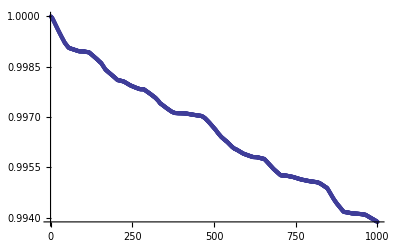

```mathematica
ListPlot[corrConfig]
```

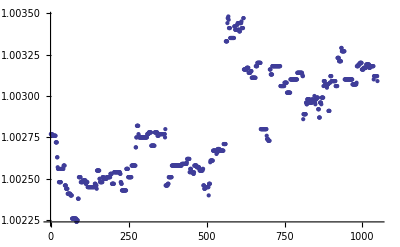

```mathematica
corrEnergy=Import["auto0.enr"]//Rest//Flatten;
ListPlot[corrEnergy]
```

## 10% RECA vs Met

```mathematica
corrConfig=Import["auto10"]//Rest//Flatten;
```

```mathematica
corrConfig//Dimensions
```

{1000}

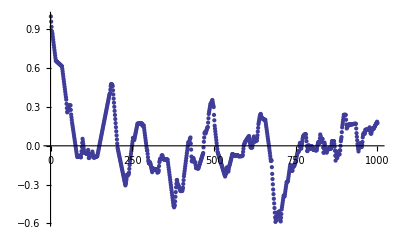

```mathematica
ListPlot[corrConfig]
```

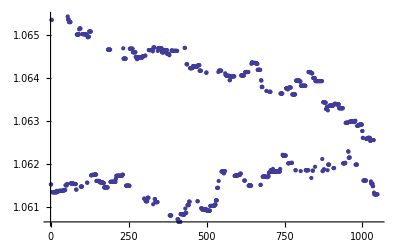

```mathematica
corrEnergy=Import["auto10.enr"]//Rest//Flatten;
ListPlot[corrEnergy]
```

## asdf

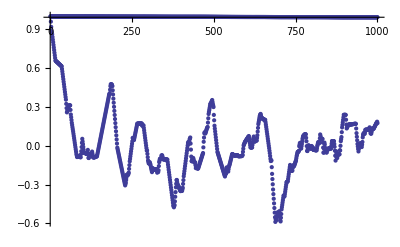

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

## new

```mathematica
{ERECA001,EMet}=(Import["auto1.enr","Table"]//Rest)ᵀ;
```

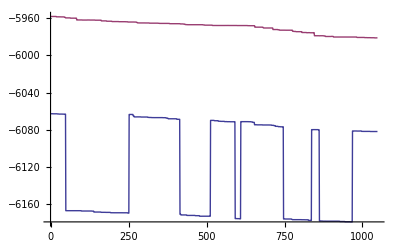

```mathematica
ListLinePlot[{ERECA001,EMet}]
```